Se introduce el sistema 1 como el sistema a analizar, notese que ya esta en el dominio de Laplace

```mathematica
Sistema1 = k/(s*(s^2+4*s+5))
```

k/(s (5+4 s+s^2))

Se introducen los coeficientes de amortiguamiento a revisar

```mathematica
Subscript[ζ, 1]=0.5
Subscript[ζ, 2]=1/√2
```

0.5

1/(√2)

Se agregan las frecuencias naturales a graficar, que se mostraran como circulos con radio ω

```mathematica
Subscript[ω, 1]=0.5
Subscript[ω, 2]=1
Subscript[ω, 3]=2
```

0.5

1

2

Se introducen las cotas a analizar en el sistema, circuos para las frecuencias naturales y lineas para los coeficientes de amortiguamientos

```mathematica
Cotas = {Dashed,
Circle[{0,0},Subscript[ω, 1]],
Circle[{0,0},Subscript[ω, 2]],
Circle[{0,0},Subscript[ω, 3]],
Red,
Line[{{-ζ ω,-ω √(1-ζ^2)},{0,0},{-ζ ω,ω √(1-ζ^2)}}/.{ω->Subscript[ω, 3], ζ->Subscript[ζ, 1]}],

Line[{{-ζ ω,-ω √(1-ζ^2)},{0,0},{-ζ ω,ω √(1-ζ^2)}}/.{ω->Subscript[ω, 2], ζ->Subscript[ζ, 2]}]}
```

{Dashing[{Small,Small}],Circle[{0,0},0.5],Circle[{0,0},1],Circle[{0,0},2],RGBColor[1,0,0],Line[{{-1.,-1.73205},{0,0},{-1.,1.73205}}],Line[{{-1/(√2),-1/(√2)},{0,0},{-1/(√2),1/(√2)}}]}

Por ultimo, se grafica el lugar geometrico del sistema con las cotas definidas anteriormente.

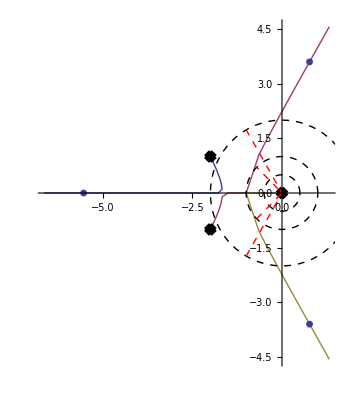

```mathematica
RootLocusPlot[Sistema1, {k,0,150},Epilog->Cotas]
```

```mathematica
Manipulate[RootLocusPlot[k*(1-.5s)/(s(s+1)),{k,0.001,a},RegionFunction->Function[{x,y,k},Sqrt[x^2+y^2]<25]],{a,0,30}]
```

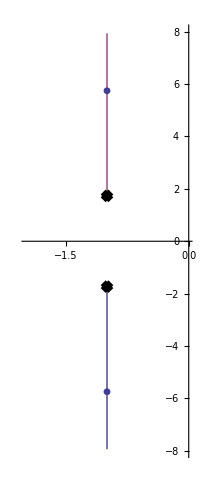

```mathematica
RootLocusPlot[k(4)/(s^2 +2s+4),{k,0,15}]
```

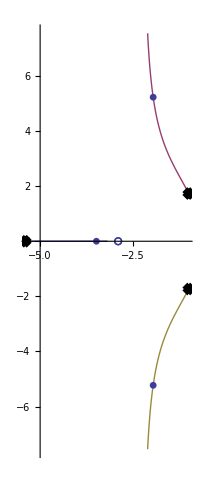

```mathematica
RootLocusPlot[k((4)/(s^2 +2s+4))((s+2.9)/(s+5.4)),{k,0,15}]
```

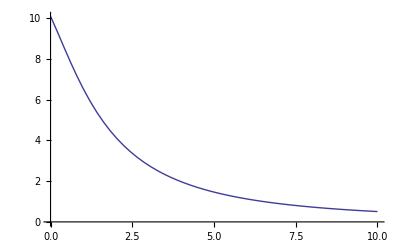

```mathematica
Plot[18.79*UnitStep[s]*((4)/(s^2 +2s+4))((s+2.9)/(s+5.4)),{s,0,10}]
```